```mathematica
Remove["Global`*"];

PDF1 = s/(2*R^2)
```

s/(2 R^2)

```mathematica
a={s∈Reals,R∈Reals,s >0, R>= 0 , s ≤ 2*R };
```

```mathematica
CDF1 = Simplify[Integrate[PDF1, s, Assumptions->a],a]
```

s^2/(4 R^2)

```mathematica
MEAN = Integrate [s * PDF1, {s, 0, 2 * R}]
```

(4 R)/3

```mathematica
VAR= Integrate [PDF1 * (s - MEAN)^2,{s, 0, 2 * R}]
```

(2 R^2)/9

```mathematica
TeXForm[PDF1]
```

\frac{s}{2 R^2}

```mathematica
TeXForm[CDF1]
```

\frac{s^2}{4 R^2}

```mathematica
CForm[PDF1]
```

s/(2.*Power(R,2))

```mathematica
CForm[CDF1]
```

Power(s,2)/(4.*Power(R,2))

```mathematica
R=1;
```

```mathematica
4
```

4

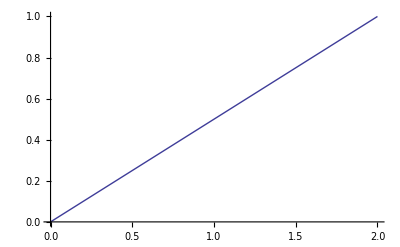

```mathematica
Plot[{PDF1},{s,0,2*R}]
```

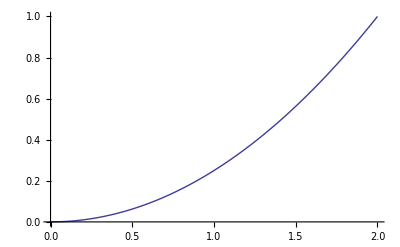

```mathematica
Plot[{CDF1},{s,0,2*R}]
```